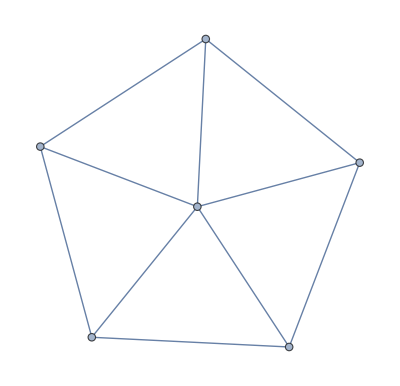

```mathematica
Graph[{1<-> 2,2<-> 3,3<-> 4,4<-> 5,1<-> 5,6<-> 1,6<-> 2,6<-> 3,6<-> 4,6<-> 5}]
```

```mathematica
BaseGenerators[ FindFullFormula[Graph[{1<-> 2,2<-> 3,3<-> 4,4<-> 5,1<-> 5,6<-> 1,6<-> 2,6<-> 3,6<-> 4,6<-> 5}]]]
```

<|4→{1♁24♁35♁6,14♁2♁35♁6,14♁25♁3♁6,13♁25♁4♁6,13♁24♁5♁6}|>

```mathematica
BaseGenerators[ FindFullFormula[WheelGraph[7]]]
```

<|3→{1♁624♁735},4→{1♁26♁35♁47,1♁25♁37♁46,1♁25♁36♁47,1♁24♁36♁57}|>

```mathematica
Map[SymbolToLabel,FindFullFormula[Graph[{1<-> 2,2<-> 3,3<-> 4,4<-> 5,1<-> 5,6<-> 1,6<-> 2,6<-> 3,6<-> 4,6<-> 5}]]]
```

{1♁2♁3♁4♁5♁6,1♁2♁35♁4♁6,1♁25♁3♁4♁6,1♁24♁3♁5♁6,1♁24♁35♁6,14♁2♁3♁5♁6,14♁2♁35♁6,14♁25♁3♁6,13♁2♁4♁5♁6,13♁25♁4♁6,13♁24♁5♁6}

```mathematica
IsRefinement[sets1_,sets2_]:=Block[{result=True,merged,allOK,s1,s2,i,current},
For[i=1,i=Length[sets2],i++,
current=sets2[i];
If[Length[Select[sets1,Length[Intersection[#,current]]==Length[current]&]]≠1,
result=False;
Break;
]
];
result
]
```

```mathematica
IsRefinement[{{1,2}},{{1},{2}}]
```

True

```mathematica
BaseGenerators[formula_]:=Block[{vars = ListofVars[formula], parts, min=100, max=-1,l, blocks=Association[], new, blocks2=Association[],ip1,deleted=0,ip2,p2},
parts =Sort[ Map[SymbolToSets[#]&,vars],Length[#1]<Length[#2]&];
Table[
l=Length[p];
If[l<min,min=l];
If[l>min,max=l];
If[!KeyExistsQ[blocks,l],blocks[l]={}];
blocks[l]=Append[blocks[l],p]
,{p,parts}];
Print[Map[SymbolToLabel[ SetsToSymbol2[#]]&,blocks[min]]];
Monitor[
For[l=max,l≥min+1,l--,
new=blocks[l];
ip1=1;
Table[
ip1+=1;
For[ip2=1,ip2<=Length[blocks[l-1]],ip2++,
p2=blocks[l-1][[ip2]];
If[IsRefinement[p2,p1],new=Select[new,#≠p1&];deleted+=1;Break[]]
];
(*Table[
If[IsRefinement[p2,p1],new=Select[new,#≠p1&];deleted+=1];
Break[]
,
{p2,blocks[l-1]}]*)
,{p1,new}];
If[new=={},
blocks=KeyDrop[blocks,{l}]
,
blocks[l]=new
];
],
{l,max,min,Length[blocks[l]],ip1,ip2,deleted }
];
Table[
blocks2[k]=Map[SymbolToLabel[ SetsToSymbol2[#]]&,blocks[k]]
,{k,Keys[blocks]}
];
blocks2
]
```

```mathematica
f1=FindFullFormula[Graph[plantri[[1]]]];
```

```mathematica
bg1=BaseGenerators[f1]
```

{957♁a36♁b18♁c24,957♁a18♁b24♁c36,925♁a37♁b18♁c46,925♁a17♁b48♁c36,917♁a68♁b24♁c35,917♁a36♁b48♁c25,846♁a37♁b19♁c25,846♁a17♁b29♁c35,735♁a68♁b19♁c24,735♁a18♁b29♁c46}

<|4→{957♁a36♁b18♁c24,957♁a18♁b24♁c36,925♁a37♁b18♁c46,925♁a17♁b48♁c36,917♁a68♁b24♁c35,917♁a36♁b48♁c25,846♁a37♁b19♁c25,846♁a17♁b29♁c35,735♁a68♁b19♁c24,735♁a18♁b29♁c46},5→{6♁79♁a18♁b24♁c35,6♁735♁9b♁a18♁c24,6c♁735♁9♁a18♁b24,6a♁735♁9♁b18♁c24,69♁8♁a17♁b24♁c35,69♁7♁a18♁b24♁c35,69♁735♁a♁b18♁c24,69♁735♁a18♁b♁c24,69♁735♁a18♁b24♁c,68♁9♁a17♁b24♁c35,5♁8b♁917♁a36♁c24,5♁8a♁917♁b24♁c36,5♁69♁a37♁b18♁c24,5♁68♁a37♁b19♁c24,5c♁8♁917♁a36♁b24,59♁8♁a17♁b24♁c36,59♁6♁a37♁b18♁c24,58♁9♁a17♁b24♁c36,58♁917♁a♁b24♁c36,58♁917♁a36♁b♁c24,58♁917♁a36♁b24♁c,58♁7♁a36♁b19♁c24,58♁6♁a37♁b19♁c24,57♁8♁a36♁b19♁c24,4♁7a♁925♁b18♁c36,4♁79♁a36♁b18♁c25,4♁69♁a37♁b18♁c25,4♁58♁a17♁b29♁c36,4♁57♁a18♁b29♁c36,4c♁7♁925♁a36♁b18,4b♁7♁925♁a18♁c36,48♁7♁a36♁b19♁c25,48♁5♁a17♁b29♁c36,47♁9♁a36♁b18♁c25,47♁925♁a♁b18♁c36,47♁925♁a36♁b18♁c,47♁925♁a18♁b♁c36,47♁8♁a36♁b19♁c25,47♁6♁a18♁b29♁c35,47♁5♁a18♁b29♁c36,46♁9♁a37♁b18♁c25,46♁7♁a18♁b29♁c35,3♁8b♁925♁a17♁c46,3♁846♁9b♁a17♁c25,3♁69♁a17♁b48♁c25,3♁58♁a17♁b29♁c46,3♁4b♁917♁a68♁c25,3♁47♁a68♁b19♁c25,3c♁846♁925♁a17♁b,3c♁59♁68♁a17♁b24,3c♁58♁6a♁917♁b24,3c♁58♁69♁a17♁b24,3c♁57♁69♁a18♁b24,3c♁4b♁68♁925♁a17,3c♁47♁6a♁925♁b18,3c♁46♁8b♁925♁a17,3c♁46♁7a♁925♁b18,3c♁46♁58♁a17♁b29,3c♁46♁57♁a18♁b29,3b♁8♁925♁a17♁c46,3b♁846♁9♁a17♁c25,3b♁846♁925♁a17♁c,3b♁846♁917♁a♁c25,3b♁7♁925♁a18♁c46,3b♁6♁957♁a18♁c24,3b♁5♁917♁a68♁c24,3b♁59♁68♁a17♁c24,3b♁58♁6a♁917♁c24,3b♁58♁69♁a17♁c24,3b♁57♁69♁a18♁c24,3b♁4♁917♁a68♁c25,3b♁4c♁68♁925♁a17,3b♁48♁6c♁925♁a17,3b♁48♁6a♁917♁c25,3b♁48♁69♁a17♁c25,3b♁47♁6c♁925♁a18,3b♁47♁69♁a18♁c25,3b♁46♁8a♁917♁c25,3b♁46♁79♁a18♁c25,3a♁846♁917♁b♁c25,3a♁5c♁68♁917♁b24,3a♁58♁6c♁917♁b24,3a♁57♁69♁b18♁c24,3a♁57♁68♁b19♁c24,3a♁4b♁68♁917♁c25,3a♁47♁6c♁925♁b18,3a♁47♁69♁b18♁c25,3a♁47♁68♁b19♁c25,3a♁46♁8b♁917♁c25,3a♁46♁79♁b18♁c25,37♁925♁a18♁b♁c46,37♁5c♁69♁a18♁b24,37♁59♁6c♁a18♁b24,37♁59♁6a♁b18♁c24,37♁58♁6a♁b19♁c24,37♁4♁a68♁b19♁c25,37♁4c♁6a♁925♁b18,37♁4b♁6c♁925♁a18,37♁4b♁69♁a18♁c25,37♁48♁6a♁b19♁c25,37♁46♁9b♁a18♁c25,37♁46♁8a♁b19♁c25,37♁46♁5c♁a18♁b29,36♁9♁a17♁b48♁c25,36♁957♁a18♁b♁c24,36♁5c♁8a♁917♁b24,36♁5c♁79♁a18♁b24,36♁59♁8b♁a17♁c24,36♁59♁7a♁b18♁c24,36♁58♁9b♁a17♁c24,36♁58♁7a♁b19♁c24,36♁57♁9b♁a18♁c24,36♁57♁8a♁b19♁c24,36♁4c♁8b♁925♁a17,36♁4c♁7a♁925♁b18,36♁4c♁58♁a17♁b29,36♁4c♁57♁a18♁b29,36♁4b♁8a♁917♁c25,36♁4b♁79♁a18♁c25,36♁48♁9b♁a17♁c25,36♁48♁7a♁b19♁c25,36♁48♁5c♁a17♁b29,36♁47♁9b♁a18♁c25,36♁47♁8a♁b19♁c25,36♁47♁5c♁a18♁b29,35♁917♁a68♁b♁c24,35♁8♁a17♁b29♁c46,35♁6c♁8a♁917♁b24,35♁6c♁79♁a18♁b24,35♁6a♁8b♁917♁c24,35♁6a♁79♁b18♁c24,35♁69♁8b♁a17♁c24,35♁69♁7a♁b18♁c24,35♁68♁9b♁a17♁c24,35♁68♁7a♁b19♁c24,35♁4c♁68♁a17♁b29,35♁48♁6c♁a17♁b29,35♁47♁6c♁a18♁b29,2♁7a♁846♁b19♁c35,2♁735♁8a♁b19♁c46,2♁6a♁917♁b48♁c35,2♁69♁a17♁b48♁c35,2♁58♁a37♁b19♁c46,2♁47♁a68♁b19♁c35,2♁3b♁957♁a18♁c46,2♁3a♁957♁b18♁c46,2c♁735♁846♁a♁b19,2c♁4b♁69♁735♁a18,2c♁4b♁58♁917♁a36,2c♁48♁6a♁735♁b19,2c♁48♁57♁a36♁b19,2c♁47♁59♁a36♁b18,2c♁47♁58♁a36♁b19,2c♁46♁735♁9b♁a18,2c♁46♁735♁8a♁b19,2c♁46♁59♁a37♁b18,2c♁46♁58♁a37♁b19,2c♁3b♁59♁846♁a17,2c♁3b♁46♁957♁a18,2c♁3a♁57♁846♁b19,2c♁3a♁46♁957♁b18,2c♁36♁59♁a17♁b48,2c♁36♁4b♁957♁a18,2c♁35♁846♁9b♁a17,2c♁35♁7a♁846♁b19,2c♁35♁6a♁917♁b48,2c♁35♁69♁a17♁b48,2c♁35♁4b♁917♁a68,2c♁35♁47♁a68♁b19,2b♁846♁917♁a♁c35,2b♁4c♁69♁735♁a18,2b♁4c♁58♁917♁a36,2b♁48♁6a♁917♁c35,2b♁48♁69♁a17♁c35,2b♁48♁5c♁917♁a36,2b♁48♁59♁a17♁c36,2b♁47♁69♁a18♁c35,2b♁47♁59♁a18♁c36,2b♁46♁8a♁917♁c35,2b♁46♁79♁a18♁c35,2b♁3♁957♁a18♁c46,2b♁3c♁59♁846♁a17,2b♁3c♁46♁957♁a18,2b♁3a♁5c♁846♁917,2b♁3a♁58♁917♁c46,2b♁37♁59♁a18♁c46,2b♁36♁4c♁957♁a18,2b♁35♁8a♁917♁c46,2b♁35♁79♁a18♁c46,2b♁35♁4c♁917♁a68,2a♁846♁917♁b♁c35,2a♁7♁846♁b19♁c35,2a♁735♁9♁b18♁c46,2a♁735♁8♁b19♁c46,2a♁735♁846♁b19♁c,2a♁6♁917♁b48♁c35,2a♁5♁917♁b48♁c36,2a♁4♁957♁b18♁c36,2a♁4c♁69♁735♁b18,2a♁4c♁68♁735♁b19,2a♁4b♁68♁917♁c35,2a♁4b♁58♁917♁c36,2a♁48♁6c♁735♁b19,2a♁48♁57♁b19♁c36,2a♁47♁69♁b18♁c35,2a♁47♁68♁b19♁c35,2a♁47♁59♁b18♁c36,2a♁47♁58♁b19♁c36,2a♁46♁8b♁917♁c35,2a♁46♁79♁b18♁c35,2a♁3♁957♁b18♁c46,2a♁3c♁57♁846♁b19,2a♁3c♁46♁957♁b18,2a♁3b♁5c♁846♁917,2a♁3b♁58♁917♁c46,2a♁37♁5c♁846♁b19,2a♁37♁59♁b18♁c46,2a♁37♁58♁b19♁c46,2a♁36♁5c♁917♁b48,2a♁36♁4c♁957♁b18,2a♁35♁8b♁917♁c46,2a♁35♁79♁b18♁c46,2a♁35♁6c♁917♁b48,29♁735♁a♁b18♁c46,29♁6♁a17♁b48♁c35,29♁4c♁6a♁735♁b18,29♁4c♁57♁a36♁b18,29♁4b♁6c♁735♁a18,29♁4b♁68♁a17♁c35,29♁4b♁58♁a17♁c36,29♁4b♁57♁a18♁c36,29♁47♁6a♁b18♁c35,29♁47♁5c♁a36♁b18,29♁46♁8b♁a17♁c35,29♁46♁7a♁b18♁c35,29♁46♁5c♁a37♁b18,29♁3b♁5c♁846♁a17,29♁3b♁58♁a17♁c46,29♁3b♁57♁a18♁c46,29♁3a♁57♁b18♁c46,29♁36♁5c♁a17♁b48,29♁35♁8b♁a17♁c46,29♁35♁7a♁b18♁c46,29♁35♁6c♁a17♁b48,25♁917♁a♁b48♁c36,25♁8♁a37♁b19♁c46,25♁4c♁8b♁917♁a36,25♁4c♁79♁a36♁b18,25♁4c♁69♁a37♁b18,25♁4c♁68♁a37♁b19,25♁4b♁8a♁917♁c36,25♁4b♁79♁a18♁c36,25♁48♁9b♁a17♁c36,25♁48♁7a♁b19♁c36,25♁48♁6c♁a37♁b19,25♁47♁9b♁a18♁c36,25♁47♁8a♁b19♁c36,25♁3c♁846♁9b♁a17,25♁3c♁7a♁846♁b19,25♁3c♁6a♁917♁b48,25♁3c♁69♁a17♁b48,25♁3c♁4b♁917♁a68,25♁3c♁47♁a68♁b19,25♁3b♁8a♁917♁c46,25♁3b♁79♁a18♁c46,25♁3b♁4c♁917♁a68,25♁3a♁8b♁917♁c46,25♁3a♁79♁b18♁c46,25♁3a♁6c♁917♁b48,25♁37♁9b♁a18♁c46,25♁37♁8a♁b19♁c46,25♁37♁4c♁a68♁b19,24♁957♁a♁b18♁c36,24♁7♁a68♁b19♁c35,24♁6c♁735♁9b♁a18,24♁6c♁735♁8a♁b19,24♁6a♁8b♁917♁c35,24♁6a♁79♁b18♁c35,24♁69♁8b♁a17♁c35,24♁69♁7a♁b18♁c35,24♁68♁9b♁a17♁c35,24♁68♁7a♁b19♁c35,24♁5c♁8b♁917♁a36,24♁5c♁79♁a36♁b18,24♁5c♁69♁a37♁b18,24♁5c♁68♁a37♁b19,24♁59♁8b♁a17♁c36,24♁59♁7a♁b18♁c36,24♁59♁6c♁a37♁b18,24♁58♁9b♁a17♁c36,24♁58♁7a♁b19♁c36,24♁58♁6c♁a37♁b19,24♁57♁9b♁a18♁c36,24♁57♁8a♁b19♁c36,24♁3c♁6a♁957♁b18,24♁3c♁57♁a68♁b19,24♁3b♁6c♁957♁a18,24♁3b♁5c♁917♁a68,24♁3a♁6c♁957♁b18,24♁37♁5c♁a68♁b19,1♁6c♁925♁a37♁b48,1♁69♁a37♁b48♁c25,1♁5c♁846♁a37♁b29,1♁58♁a37♁b29♁c46,1♁4c♁735♁a68♁b29,1♁47♁a68♁b29♁c35,1♁3c♁957♁a68♁b24,1♁3b♁957♁a68♁c24,1♁2c♁957♁a36♁b48,1♁2a♁957♁b48♁c36,1c♁8♁957♁a36♁b24,1c♁846♁925♁a37♁b,1c♁7♁925♁a36♁b48,1c♁735♁9♁a68♁b24,1c♁735♁846♁a♁b29,1c♁6♁925♁a37♁b48,1c♁69♁735♁8a♁b24,1c♁5♁846♁a37♁b29,1c♁59♁68♁a37♁b24,1c♁58♁79♁a36♁b24,1c♁58♁69♁a37♁b24,1c♁4♁735♁a68♁b29,1c♁4b♁68♁925♁a37,1c♁48♁6a♁735♁b29,1c♁48♁57♁a36♁b29,1c♁47♁8b♁925♁a36,1c♁47♁58♁a36♁b29,1c♁46♁8b♁925♁a37,1c♁46♁735♁8a♁b29,1c♁46♁58♁a37♁b29,1c♁3♁957♁a68♁b24,1c♁3b♁7a♁846♁925,1c♁3b♁47♁925♁a68,1c♁3a♁68♁957♁b24,1c♁3a♁57♁846♁b29,1c♁37♁6a♁925♁b48,1c♁37♁59♁a68♁b24,1c♁37♁4b♁925♁a68,1c♁36♁8a♁957♁b24,1c♁36♁7a♁925♁b48,1c♁35♁7a♁846♁b29,1c♁35♁79♁a68♁b24,1c♁35♁47♁a68♁b29,1c♁2♁957♁a36♁b48,1c♁2b♁59♁846♁a37,1c♁2b♁48♁957♁a36,1c♁2b♁3a♁846♁957,1c♁2a♁735♁846♁9b,1c♁2a♁69♁735♁b48,1c♁2a♁3b♁846♁957,1c♁2a♁36♁957♁b48,1c♁29♁6a♁735♁b48,1c♁29♁57♁a36♁b48,1c♁29♁4b♁735♁a68,1c♁25♁846♁9b♁a37,1c♁25♁79♁a36♁b48,1c♁25♁69♁a37♁b48,1c♁24♁8b♁957♁a36,1c♁24♁735♁9b♁a68,1c♁24♁3b♁957♁a68,1b♁846♁925♁a37♁c,1b♁69♁735♁8a♁c24,1b♁59♁68♁a37♁c24,1b♁58♁79♁a36♁c24,1b♁58♁69♁a37♁c24,1b♁4c♁68♁925♁a37,1b♁48♁7a♁925♁c36,1b♁48♁79♁a36♁c25,1b♁48♁6c♁925♁a37,1b♁48♁69♁a37♁c25,1b♁47♁8a♁925♁c36,1b♁3♁957♁a68♁c24,1b♁3c♁7a♁846♁925,1b♁3c♁47♁925♁a68,1b♁3a♁79♁846♁c25,1b♁3a♁68♁957♁c24,1b♁37♁8a♁925♁c46,1b♁37♁59♁a68♁c24,1b♁37♁4c♁925♁a68,1b♁36♁8a♁957♁c24,1b♁35♁79♁a68♁c24,1b♁2c♁59♁846♁a37,1b♁2c♁48♁957♁a36,1b♁2c♁3a♁846♁957,1b♁2a♁79♁846♁c35,1b♁2a♁48♁957♁c36,1b♁2a♁3c♁846♁957,1b♁29♁7a♁846♁c35,1b♁29♁735♁8a♁c46,1b♁29♁5c♁846♁a37,1b♁29♁58♁a37♁c46,1b♁29♁4c♁735♁a68,1b♁29♁47♁a68♁c35,1b♁24♁8a♁957♁c36,1b♁24♁79♁a68♁c35,1b♁24♁3c♁957♁a68,1a♁735♁846♁b29♁c,1a♁69♁735♁8b♁c24,1a♁68♁79♁b24♁c35,1a♁68♁735♁9b♁c24,1a♁58♁79♁b24♁c36,1a♁4c♁68♁735♁b29,1a♁48♁6c♁735♁b29,1a♁48♁57♁b29♁c36,1a♁47♁8b♁925♁c36,1a♁47♁68♁b29♁c35,1a♁47♁58♁b29♁c36,1a♁3c♁68♁957♁b24,1a♁3c♁57♁846♁b29,1a♁3b♁79♁846♁c25,1a♁3b♁68♁957♁c24,1a♁37♁8b♁925♁c46,1a♁37♁846♁9b♁c25,1a♁37♁6c♁925♁b48,1a♁37♁69♁b48♁c25,1a♁37♁5c♁846♁b29,1a♁37♁58♁b29♁c46,1a♁36♁8b♁957♁c24,1a♁36♁79♁b48♁c25,1a♁2♁957♁b48♁c36,1a♁2c♁735♁846♁9b,1a♁2c♁69♁735♁b48,1a♁2c♁3b♁846♁957,1a♁2c♁36♁957♁b48,1a♁2b♁79♁846♁c35,1a♁2b♁48♁957♁c36,1a♁2b♁3c♁846♁957,1a♁29♁735♁8b♁c46,1a♁29♁6c♁735♁b48,1a♁29♁57♁b48♁c36,1a♁25♁79♁b48♁c36,1a♁24♁8b♁957♁c36,19♁735♁a68♁b24♁c,19♁6♁a37♁b48♁c25,19♁6c♁735♁8a♁b24,19♁6a♁735♁8b♁c24,19♁68♁7a♁b24♁c35,19♁5c♁68♁a37♁b24,19♁58♁7a♁b24♁c36,19♁58♁6c♁a37♁b24,19♁57♁8b♁a36♁c24,19♁57♁8a♁b24♁c36,19♁4b♁68♁a37♁c25,19♁47♁8b♁a36♁c25,19♁46♁8b♁a37♁c25,19♁3c♁57♁a68♁b24,19♁3b♁7a♁846♁c25,19♁3b♁57♁a68♁c24,19♁3b♁47♁a68♁c25,19♁37♁6a♁b48♁c25,19♁37♁5c♁a68♁b24,19♁37♁4b♁a68♁c25,19♁36♁7a♁b48♁c25,19♁2c♁6a♁735♁b48,19♁2c♁57♁a36♁b48,19♁2c♁4b♁735♁a68,19♁2b♁7a♁846♁c35,19♁2b♁735♁8a♁c46,19♁2b♁5c♁846♁a37,19♁2b♁58♁a37♁c46,19♁2b♁4c♁735♁a68,19♁2b♁47♁a68♁c35,19♁2a♁735♁8b♁c46,19♁2a♁6c♁735♁b48,19♁2a♁57♁b48♁c36,19♁25♁8b♁a37♁c46,19♁25♁7a♁b48♁c36,19♁25♁6c♁a37♁b48,18♁957♁a36♁b24♁c,18♁6a♁79♁b24♁c35,18♁6a♁735♁9b♁c24,18♁69♁7a♁b24♁c35,18♁5♁a37♁b29♁c46,18♁5c♁79♁a36♁b24,18♁5c♁69♁a37♁b24,18♁59♁7a♁b24♁c36,18♁59♁6c♁a37♁b24,18♁57♁9b♁a36♁c24,18♁4c♁6a♁735♁b29,18♁4c♁57♁a36♁b29,18♁4b♁7a♁925♁c36,18♁4b♁79♁a36♁c25,18♁4b♁6c♁925♁a37,18♁4b♁69♁a37♁c25,18♁47♁9b♁a36♁c25,18♁47♁6a♁b29♁c35,18♁47♁5c♁a36♁b29,18♁46♁9b♁a37♁c25,18♁46♁7a♁b29♁c35,18♁46♁5c♁a37♁b29,18♁3c♁6a♁957♁b24,18♁3b♁7a♁925♁c46,18♁3b♁6a♁957♁c24,18♁3a♁6c♁957♁b24,18♁3a♁57♁b29♁c46,18♁35♁7a♁b29♁c46,18♁2c♁4b♁957♁a36,18♁2b♁59♁a37♁c46,18♁2b♁4c♁957♁a36,18♁2b♁3a♁957♁c46,18♁2a♁735♁9b♁c46,18♁2a♁4b♁957♁c36,18♁2a♁3b♁957♁c46,18♁25♁9b♁a37♁c46,17♁925♁a36♁b48♁c,17♁69♁8a♁b24♁c35,17♁59♁8b♁a36♁c24,17♁59♁8a♁b24♁c36,17♁58♁9b♁a36♁c24,17♁4♁a68♁b29♁c35,17♁4c♁8b♁925♁a36,17♁4c♁58♁a36♁b29,17♁4b♁8a♁925♁c36,17♁48♁9b♁a36♁c25,17♁48♁6a♁b29♁c35,17♁48♁5c♁a36♁b29,17♁46♁8a♁b29♁c35,17♁3c♁6a♁925♁b48,17♁3c♁59♁a68♁b24,17♁3c♁4b♁925♁a68,17♁3b♁8a♁925♁c46,17♁3b♁59♁a68♁c24,17♁3b♁4c♁925♁a68,17♁3a♁8b♁925♁c46,17♁3a♁846♁9b♁c25,17♁3a♁6c♁925♁b48,17♁3a♁69♁b48♁c25,17♁3a♁5c♁846♁b29,17♁3a♁58♁b29♁c46,17♁35♁9b♁a68♁c24,17♁35♁8a♁b29♁c46,17♁35♁4c♁a68♁b29,17♁2c♁59♁a36♁b48,17♁2a♁846♁9b♁c35,17♁2a♁69♁b48♁c35,17♁2a♁59♁b48♁c36,17♁29♁6a♁b48♁c35,17♁29♁5c♁a36♁b48,17♁29♁4b♁a68♁c35,17♁24♁9b♁a68♁c35},6→{3♁4b♁68♁9♁a17♁c25,3♁46♁8b♁9♁a17♁c25,3c♁46♁7♁925♁a18♁b,3a♁5♁68♁917♁b♁c24,37♁59♁6♁a18♁b♁c24,37♁4♁6a♁9♁b18♁c25,36♁5♁8a♁917♁b♁c24,36♁5c♁8♁9♁a17♁b24,36♁4♁7a♁9♁b18♁c25,36♁4c♁7♁925♁a18♁b,35♁6♁79♁a18♁b♁c24,35♁6c♁8♁9♁a17♁b24,2♁48♁6a♁7♁b19♁c35,2♁46♁7♁8a♁b19♁c35,2♁3c♁48♁57♁6a♁b19,2♁3c♁47♁58♁6a♁b19,2♁3c♁46♁58♁7a♁b19,2♁3c♁46♁57♁8a♁b19,2♁3a♁57♁8♁b19♁c46,2♁3a♁48♁57♁6c♁b19,2♁3a♁47♁58♁6c♁b19,2♁35♁7a♁8♁b19♁c46,2♁35♁48♁6c♁7a♁b19,2♁35♁47♁6c♁8a♁b19,2c♁46♁735♁9♁a♁b18,2c♁3♁4b♁59♁68♁a17,2c♁3♁4b♁58♁69♁a17,2c♁3♁46♁59♁8b♁a17,2c♁3♁46♁58♁9b♁a17,2c♁3b♁47♁59♁6♁a18,2c♁3b♁46♁58♁9♁a17,2c♁3b♁46♁58♁917♁a,2c♁3a♁46♁58♁917♁b,2c♁37♁4b♁59♁6♁a18,2c♁37♁46♁59♁a18♁b,2c♁36♁4b♁58♁9♁a17,2c♁36♁47♁59♁a18♁b,2c♁35♁846♁917♁a♁b,2c♁35♁4b♁6♁79♁a18,2c♁35♁4b♁68♁9♁a17,2c♁35♁47♁6♁9b♁a18,2c♁35♁47♁6a♁9♁b18,2c♁35♁47♁69♁a♁b18,2c♁35♁47♁69♁a18♁b,2c♁35♁46♁8b♁9♁a17,2c♁35♁46♁8b♁917♁a,2c♁35♁46♁8a♁917♁b,2c♁35♁46♁7a♁9♁b18,2c♁35♁46♁79♁a♁b18,2c♁35♁46♁79♁a18♁b,2b♁48♁5♁917♁a♁c36,2b♁3♁59♁8♁a17♁c46,2b♁3♁4c♁59♁68♁a17,2b♁3♁4c♁58♁69♁a17,2b♁3c♁46♁58♁917♁a,2b♁3a♁4c♁5♁68♁917,2b♁3a♁48♁5♁6c♁917,2b♁36♁4c♁5♁8a♁917,2b♁36♁4c♁59♁8♁a17,2b♁35♁4c♁69♁8♁a17,2b♁35♁48♁6c♁917♁a,2a♁3c♁4♁57♁69♁b18,2a♁3c♁46♁58♁917♁b,2a♁3c♁46♁58♁7♁b19,2a♁3b♁4c♁5♁68♁917,2a♁3b♁48♁5♁6c♁917,2a♁37♁4♁5c♁69♁b18,2a♁37♁46♁5c♁9♁b18,2a♁36♁4♁5c♁79♁b18,2a♁36♁4c♁5♁8b♁917,2a♁36♁4c♁58♁917♁b,2a♁36♁4c♁58♁7♁b19,2a♁36♁4c♁57♁8♁b19,2a♁36♁48♁5c♁7♁b19,2a♁36♁47♁5c♁9♁b18,2a♁36♁47♁5c♁8♁b19,2a♁35♁4c♁68♁917♁b,2a♁35♁47♁6c♁9♁b18,2a♁35♁47♁6c♁8♁b19,29♁4♁57♁a♁b18♁c36,29♁4b♁6♁7♁a18♁c35,29♁3c♁4♁57♁6a♁b18,29♁3c♁46♁57♁a♁b18,29♁3b♁47♁5c♁6♁a18,29♁3b♁46♁5c♁7♁a18,29♁37♁4♁5c♁6a♁b18,29♁37♁4b♁5c♁6♁a18,29♁36♁4♁5c♁7a♁b18,29♁36♁4b♁5c♁7♁a18,29♁35♁47♁6c♁a♁b18,25♁4♁79♁a♁b18♁c36,25♁4c♁7♁8♁a36♁b19,25♁3♁8♁9b♁a17♁c46,25♁3♁4c♁69♁8b♁a17,25♁3♁4c♁68♁9b♁a17,25♁3c♁846♁917♁a♁b,25♁3c♁4♁6a♁79♁b18,25♁3c♁4♁69♁7a♁b18,25♁3c♁4b♁69♁7♁a18,25♁3c♁48♁6a♁7♁b19,25♁3c♁47♁69♁a♁b18,25♁3c♁47♁69♁a18♁b,25♁3c♁46♁8b♁917♁a,25♁3c♁46♁8a♁917♁b,25♁3c♁46♁7♁9b♁a18,25♁3c♁46♁7♁8a♁b19,25♁3c♁46♁79♁a♁b18,25♁3c♁46♁79♁a18♁b,25♁3b♁4c♁69♁8♁a17,25♁3b♁4c♁69♁7♁a18,25♁3b♁48♁6c♁917♁a,25♁3a♁4c♁68♁917♁b,25♁3a♁47♁6c♁8♁b19,25♁37♁4c♁69♁a18♁b,25♁36♁4c♁8♁9b♁a17,25♁36♁4c♁8a♁917♁b,25♁36♁4c♁7♁9b♁a18,25♁36♁4c♁7♁8a♁b19,25♁36♁4c♁7a♁8♁b19,25♁36♁4c♁79♁a18♁b,24♁6♁7♁9b♁a18♁c35,24♁6c♁735♁9♁a♁b18,24♁5♁8b♁917♁a♁c36,24♁5c♁7♁8♁a36♁b19,24♁3c♁58♁6a♁7♁b19,24♁3c♁57♁69♁a♁b18,24♁3b♁5♁6c♁8a♁917,24♁3b♁5c♁6♁79♁a18,24♁3b♁5c♁69♁8♁a17,24♁3b♁5c♁69♁7♁a18,24♁3b♁5c♁68♁9♁a17,24♁3b♁59♁6c♁8♁a17,24♁3b♁58♁6c♁9♁a17,24♁3b♁58♁6c♁917♁a,24♁3a♁5♁6c♁8b♁917,24♁3a♁57♁6c♁8♁b19,24♁37♁5c♁6♁9b♁a18,24♁37♁5c♁6a♁9♁b18,24♁36♁5c♁8♁9b♁a17,24♁36♁5c♁8b♁9♁a17,24♁36♁5c♁7♁9b♁a18,24♁36♁5c♁7♁8a♁b19,24♁36♁5c♁7a♁9♁b18,24♁36♁5c♁7a♁8♁b19,24♁35♁6c♁8♁9b♁a17,24♁35♁6c♁8b♁9♁a17,24♁35♁6c♁8b♁917♁a,24♁35♁6c♁7a♁9♁b18,24♁35♁6c♁7a♁8♁b19,24♁35♁6c♁79♁a♁b18,1♁4c♁5♁68♁a37♁b29,1♁48♁5♁6c♁a37♁b29,1♁3c♁4♁57♁a68♁b29,1♁3c♁48♁57♁6a♁b29,1♁3c♁47♁58♁6a♁b29,1♁3a♁4c♁57♁68♁b29,1♁3a♁48♁57♁6c♁b29,1♁3a♁47♁5c♁68♁b29,1♁3a♁47♁58♁6c♁b29,1♁37♁4♁5c♁a68♁b29,1♁37♁4c♁58♁6a♁b29,1♁37♁48♁5c♁6a♁b29,1♁2♁3c♁6a♁957♁b48,1♁2♁3a♁6c♁957♁b48,1♁2c♁59♁6♁a37♁b48,1♁2c♁4b♁59♁68♁a37,1♁2c♁4b♁58♁69♁a37,1♁2c♁3♁4b♁957♁a68,1♁2c♁3b♁48♁6a♁957,1♁2c♁3b♁47♁59♁a68,1♁2c♁3a♁57♁69♁b48,1♁2c♁3a♁4b♁68♁957,1♁2c♁37♁59♁6a♁b48,1♁2c♁37♁4b♁59♁a68,1♁2b♁4c♁59♁68♁a37,1♁2b♁4c♁58♁69♁a37,1♁2b♁48♁5c♁69♁a37,1♁2b♁48♁59♁6c♁a37,1♁2b♁3♁4c♁957♁a68,1♁2b♁3c♁48♁6a♁957,1♁2b♁3c♁47♁59♁a68,1♁2b♁3a♁4c♁68♁957,1♁2b♁3a♁48♁6c♁957,1♁2b♁37♁4c♁59♁a68,1♁2a♁3c♁57♁69♁b48,1♁2a♁3c♁4b♁68♁957,1♁2a♁3b♁4c♁68♁957,1♁2a♁3b♁48♁6c♁957,1♁2a♁37♁5c♁69♁b48,1♁2a♁37♁59♁6c♁b48,1♁29♁5c♁6♁a37♁b48,1♁29♁4b♁5c♁68♁a37,1♁29♁4b♁58♁6c♁a37,1♁29♁3c♁57♁6a♁b48,1♁29♁3c♁4b♁57♁a68,1♁29♁3b♁4c♁57♁a68,1♁29♁3b♁47♁5c♁a68,1♁29♁3a♁57♁6c♁b48,1♁29♁37♁5c♁6a♁b48,1♁29♁37♁4b♁5c♁a68,1c♁3b♁48♁6a♁7♁925,1c♁3b♁46♁7♁8a♁925,1c♁3a♁57♁69♁8♁b24,1c♁3a♁47♁68♁925♁b,1c♁3a♁47♁5♁68♁b29,1c♁37♁58♁6a♁9♁b24,1c♁37♁4♁58♁6a♁b29,1c♁37♁46♁8a♁925♁b,1c♁36♁59♁7a♁8♁b24,1c♁36♁58♁7a♁9♁b24,1c♁36♁4♁58♁7a♁b29,1c♁36♁4♁57♁8a♁b29,1c♁36♁4b♁7♁8a♁925,1c♁36♁48♁5♁7a♁b29,1c♁36♁47♁8a♁925♁b,1c♁36♁47♁5♁8a♁b29,1c♁35♁69♁7a♁8♁b24,1c♁35♁68♁7a♁9♁b24,1c♁2♁3b♁48♁6a♁957,1c♁2♁3b♁46♁8a♁957,1c♁2♁3a♁57♁69♁b48,1c♁2♁3a♁46♁8b♁957,1c♁2♁35♁6a♁79♁b48,1c♁2♁35♁69♁7a♁b48,1c♁2b♁48♁69♁735♁a,1c♁2b♁48♁5♁69♁a37,1c♁2b♁47♁59♁8♁a36,1c♁2b♁3♁47♁59♁a68,1c♁2b♁3♁46♁8a♁957,1c♁2b♁3a♁48♁57♁69,1c♁2b♁3a♁47♁59♁68,1c♁2b♁3a♁47♁58♁69,1c♁2b♁3a♁46♁58♁79,1c♁2b♁37♁48♁59♁6a,1c♁2b♁37♁46♁59♁8a,1c♁2b♁36♁48♁59♁7a,1c♁2b♁36♁47♁59♁8a,1c♁2b♁35♁79♁846♁a,1c♁2b♁35♁48♁6a♁79,1c♁2b♁35♁48♁69♁7a,1c♁2b♁35♁47♁69♁8a,1c♁2b♁35♁46♁79♁8a,1c♁2a♁4b♁68♁735♁9,1c♁2a♁46♁735♁8b♁9,1c♁2a♁3♁4b♁68♁957,1c♁2a♁3♁46♁8b♁957,1c♁2a♁3b♁48♁57♁69,1c♁2a♁3b♁47♁59♁68,1c♁2a♁3b♁47♁58♁69,1c♁2a♁3b♁46♁58♁79,1c♁2a♁37♁59♁846♁b,1c♁2a♁37♁59♁6♁b48,1c♁2a♁37♁4b♁59♁68,1c♁2a♁37♁4b♁58♁69,1c♁2a♁37♁46♁59♁8b,1c♁2a♁37♁46♁58♁9b,1c♁2a♁36♁4b♁58♁79,1c♁2a♁36♁48♁57♁9b,1c♁2a♁36♁47♁59♁8b,1c♁2a♁36♁47♁58♁9b,1c♁2a♁35♁79♁846♁b,1c♁2a♁35♁6♁79♁b48,1c♁2a♁35♁4b♁68♁79,1c♁2a♁35♁47♁69♁8b,1c♁2a♁35♁47♁68♁9b,1c♁2a♁35♁46♁79♁8b,1c♁29♁4b♁58♁7♁a36,1c♁29♁4b♁58♁6♁a37,1c♁29♁46♁735♁8b♁a,1c♁29♁3b♁57♁846♁a,1c♁29♁3b♁4♁57♁a68,1c♁29♁3b♁48♁57♁6a,1c♁29♁3b♁47♁58♁6a,1c♁29♁3b♁46♁58♁7a,1c♁29♁3b♁46♁57♁8a,1c♁29♁3a♁4b♁57♁68,1c♁29♁3a♁46♁57♁8b,1c♁29♁37♁4b♁58♁6a,1c♁29♁36♁4b♁58♁7a,1c♁29♁36♁4b♁57♁8a,1c♁29♁35♁6♁7a♁b48,1c♁29♁35♁4b♁68♁7a,1c♁29♁35♁47♁6a♁8b,1c♁29♁35♁46♁7a♁8b,1c♁25♁48♁7♁9b♁a36,1c♁25♁47♁8♁9b♁a36,1c♁25♁3♁4b♁79♁a68,1c♁25♁3♁47♁9b♁a68,1c♁25♁3b♁79♁846♁a,1c♁25♁3b♁4♁79♁a68,1c♁25♁3b♁48♁6a♁79,1c♁25♁3b♁48♁69♁7a,1c♁25♁3b♁47♁69♁8a,1c♁25♁3b♁46♁79♁8a,1c♁25♁3a♁79♁846♁b,1c♁25♁3a♁4b♁68♁79,1c♁25♁3a♁47♁69♁8b,1c♁25♁3a♁47♁68♁9b,1c♁25♁3a♁46♁79♁8b,1c♁25♁37♁4♁9b♁a68,1c♁25♁37♁4b♁69♁8a,1c♁25♁37♁48♁6a♁9b,1c♁25♁37♁46♁8a♁9b,1c♁25♁36♁4b♁79♁8a,1c♁25♁36♁48♁7a♁9b,1c♁25♁36♁47♁8a♁9b,1c♁24♁6a♁735♁8b♁9,1c♁24♁69♁735♁8b♁a,1c♁24♁5♁69♁8b♁a37,1c♁24♁5♁68♁9b♁a37,1c♁24♁59♁6♁8b♁a37,1c♁24♁58♁7♁9b♁a36,1c♁24♁58♁6♁9b♁a37,1c♁24♁57♁8♁9b♁a36,1c♁24♁3b♁59♁68♁7a,1c♁24♁3b♁58♁6a♁79,1c♁24♁3b♁58♁69♁7a,1c♁24♁3b♁57♁69♁8a,1c♁24♁3a♁57♁69♁8b,1c♁24♁3a♁57♁68♁9b,1c♁24♁37♁59♁6a♁8b,1c♁24♁37♁58♁6a♁9b,1c♁24♁36♁59♁7a♁8b,1c♁24♁36♁58♁7a♁9b,1c♁24♁36♁57♁8a♁9b,1c♁24♁35♁6a♁79♁8b,1c♁24♁35♁69♁7a♁8b,1c♁24♁35♁68♁7a♁9b,1b♁48♁7♁925♁a36♁c,1b♁3♁4♁79♁a68♁c25,1b♁3♁47♁69♁8a♁c25,1b♁3♁46♁79♁8a♁c25,1b♁3c♁48♁6a♁7♁925,1b♁3c♁46♁7♁8a♁925,1b♁3a♁47♁68♁925♁c,1b♁37♁4♁69♁8a♁c25,1b♁37♁48♁6a♁925♁c,1b♁36♁4♁79♁8a♁c25,1b♁36♁4c♁7♁8a♁925,1b♁2♁48♁6a♁79♁c35,1b♁2♁48♁69♁7a♁c35,1b♁2♁47♁69♁8a♁c35,1b♁2♁46♁79♁8a♁c35,1b♁2♁3♁8a♁957♁c46,1b♁2♁3c♁48♁6a♁957,1b♁2♁3c♁46♁8a♁957,1b♁2♁3a♁58♁79♁c46,1b♁2♁3a♁48♁6c♁957,1b♁2♁35♁79♁8a♁c46,1b♁2c♁48♁69♁735♁a,1b♁2c♁3♁47♁59♁a68,1b♁2c♁3♁46♁8a♁957,1b♁2c♁3a♁48♁57♁69,1b♁2c♁3a♁47♁59♁68,1b♁2c♁3a♁47♁58♁69,1b♁2c♁3a♁46♁58♁79,1b♁2c♁37♁48♁59♁6a,1b♁2c♁37♁46♁59♁8a,1b♁2c♁36♁48♁59♁7a,1b♁2c♁36♁47♁59♁8a,1b♁2c♁35♁79♁846♁a,1b♁2c♁35♁48♁6a♁79,1b♁2c♁35♁48♁69♁7a,1b♁2c♁35♁47♁69♁8a,1b♁2c♁35♁46♁79♁8a,1b♁2a♁4♁58♁79♁c36,1b♁2a♁48♁69♁7♁c35,1b♁2a♁48♁69♁735♁c,1b♁2a♁3♁58♁79♁c46,1b♁2a♁3♁4c♁68♁957,1b♁2a♁3c♁48♁57♁69,1b♁2a♁3c♁47♁59♁68,1b♁2a♁3c♁47♁58♁69,1b♁2a♁3c♁46♁58♁79,1b♁2a♁37♁59♁846♁c,1b♁2a♁37♁4c♁59♁68,1b♁2a♁37♁4c♁58♁69,1b♁2a♁37♁48♁5c♁69,1b♁2a♁37♁48♁59♁6c,1b♁2a♁36♁4c♁58♁79,1b♁2a♁36♁48♁5c♁79,1b♁2a♁35♁4c♁68♁79,1b♁2a♁35♁48♁6c♁79,1b♁29♁735♁846♁a♁c,1b♁29♁4♁58♁7a♁c36,1b♁29♁4♁57♁8a♁c36,1b♁29♁4c♁58♁7♁a36,1b♁29♁48♁6c♁735♁a,1b♁29♁48♁6a♁7♁c35,1b♁29♁48♁6a♁735♁c,1b♁29♁48♁5c♁7♁a36,1b♁29♁48♁57♁a♁c36,1b♁29♁48♁57♁a36♁c,1b♁29♁47♁58♁a♁c36,1b♁29♁47♁58♁a36♁c,1b♁29♁46♁7♁8a♁c35,1b♁29♁3c♁57♁846♁a,1b♁29♁3c♁4♁57♁a68,1b♁29♁3c♁48♁57♁6a,1b♁29♁3c♁47♁58♁6a,1b♁29♁3c♁46♁58♁7a,1b♁29♁3c♁46♁57♁8a,1b♁29♁3a♁57♁846♁c,1b♁29♁3a♁4c♁57♁68,1b♁29♁3a♁48♁57♁6c,1b♁29♁3a♁47♁5c♁68,1b♁29♁3a♁47♁58♁6c,1b♁29♁37♁4♁5c♁a68,1b♁29♁37♁4c♁58♁6a,1b♁29♁37♁48♁5c♁6a,1b♁29♁37♁46♁5c♁8a,1b♁29♁36♁4c♁58♁7a,1b♁29♁36♁4c♁57♁8a,1b♁29♁36♁48♁5c♁7a,1b♁29♁36♁47♁5c♁8a,1b♁29♁35♁4c♁68♁7a,1b♁29♁35♁48♁6c♁7a,1b♁29♁35♁47♁6c♁8a,1b♁25♁4♁79♁8a♁c36,1b♁25♁48♁79♁a♁c36,1b♁25♁3♁79♁8a♁c46,1b♁25♁3♁4c♁79♁a68,1b♁25♁3c♁79♁846♁a,1b♁25♁3c♁4♁79♁a68,1b♁25♁3c♁48♁6a♁79,1b♁25♁3c♁48♁69♁7a,1b♁25♁3c♁47♁69♁8a,1b♁25♁3c♁46♁79♁8a,1b♁25♁3a♁4c♁68♁79,1b♁25♁3a♁48♁6c♁79,1b♁25♁37♁4c♁69♁8a,1b♁25♁36♁4c♁79♁8a,1b♁24♁69♁7♁8a♁c35,1b♁24♁58♁79♁a♁c36,1b♁24♁3c♁59♁68♁7a,1b♁24♁3c♁58♁6a♁79,1b♁24♁3c♁58♁69♁7a,1b♁24♁3c♁57♁69♁8a,1b♁24♁3a♁5c♁68♁79,1b♁24♁3a♁58♁6c♁79,1b♁24♁37♁5c♁69♁8a,1b♁24♁37♁59♁6c♁8a,1b♁24♁36♁5c♁79♁8a,1b♁24♁35♁6c♁79♁8a,1a♁68♁735♁9♁b24♁c,1a♁3♁4b♁68♁79♁c25,1a♁3♁47♁69♁8b♁c25,1a♁3♁47♁68♁9b♁c25,1a♁3♁46♁79♁8b♁c25,1a♁3c♁47♁68♁925♁b,1a♁3b♁58♁6♁79♁c24,1a♁3b♁47♁68♁9♁c25,1a♁3b♁47♁68♁925♁c,1a♁37♁846♁925♁b♁c,1a♁37♁5c♁68♁9♁b24,1a♁37♁59♁6♁8b♁c24,1a♁37♁59♁68♁b♁c24,1a♁37♁59♁68♁b24♁c,1a♁37♁58♁6♁9b♁c24,1a♁37♁58♁6c♁9♁b24,1a♁37♁58♁69♁b♁c24,1a♁37♁58♁69♁b24♁c,1a♁37♁4c♁68♁925♁b,1a♁37♁4b♁68♁9♁c25,1a♁37♁4b♁68♁925♁c,1a♁37♁46♁8b♁9♁c25,1a♁36♁58♁79♁b♁c24,1a♁36♁47♁8b♁9♁c25,1a♁35♁6♁79♁8b♁c24,1a♁35♁68♁79♁b♁c24,1a♁2♁6♁79♁b48♁c35,1a♁2♁47♁69♁8b♁c35,1a♁2♁46♁79♁8b♁c35,1a♁2♁3♁8b♁957♁c46,1a♁2♁3c♁57♁69♁b48,1a♁2♁3c♁46♁8b♁957,1a♁2♁3b♁58♁79♁c46,1a♁2♁3b♁48♁6c♁957,1a♁2♁35♁79♁8b♁c46,1a♁2♁35♁6c♁79♁b48,1a♁2c♁4b♁68♁735♁9,1a♁2c♁46♁735♁8b♁9,1a♁2c♁3♁4b♁68♁957,1a♁2c♁3♁46♁8b♁957,1a♁2c♁3b♁48♁57♁69,1a♁2c♁3b♁47♁59♁68,1a♁2c♁3b♁47♁58♁69,1a♁2c♁3b♁46♁58♁79,1a♁2c♁37♁59♁846♁b,1a♁2c♁37♁59♁6♁b48,1a♁2c♁37♁4b♁59♁68,1a♁2c♁37♁4b♁58♁69,1a♁2c♁37♁46♁59♁8b,1a♁2c♁37♁46♁58♁9b,1a♁2c♁36♁4b♁58♁79,1a♁2c♁36♁48♁57♁9b,1a♁2c♁36♁47♁59♁8b,1a♁2c♁36♁47♁58♁9b,1a♁2c♁35♁79♁846♁b,1a♁2c♁35♁6♁79♁b48,1a♁2c♁35♁4b♁68♁79,1a♁2c♁35♁47♁69♁8b,1a♁2c♁35♁47♁68♁9b,1a♁2c♁35♁46♁79♁8b,1a♁2b♁48♁69♁735♁c,1a♁2b♁3♁58♁79♁c46,1a♁2b♁3♁4c♁68♁957,1a♁2b♁3c♁48♁57♁69,1a♁2b♁3c♁47♁59♁68,1a♁2b♁3c♁47♁58♁69,1a♁2b♁3c♁46♁58♁79,1a♁2b♁37♁59♁846♁c,1a♁2b♁37♁4c♁59♁68,1a♁2b♁37♁4c♁58♁69,1a♁2b♁37♁48♁5c♁69,1a♁2b♁37♁48♁59♁6c,1a♁2b♁36♁4c♁58♁79,1a♁2b♁36♁48♁5c♁79,1a♁2b♁35♁4c♁68♁79,1a♁2b♁35♁48♁6c♁79,1a♁29♁4b♁68♁735♁c,1a♁29♁47♁6♁8b♁c35,1a♁29♁3c♁4b♁57♁68,1a♁29♁3c♁46♁57♁8b,1a♁29♁3b♁57♁846♁c,1a♁29♁3b♁4c♁57♁68,1a♁29♁3b♁48♁57♁6c,1a♁29♁3b♁47♁5c♁68,1a♁29♁3b♁47♁58♁6c,1a♁29♁37♁5c♁6♁b48,1a♁29♁37♁4b♁5c♁68,1a♁29♁37♁4b♁58♁6c,1a♁29♁37♁46♁5c♁8b,1a♁29♁36♁4c♁57♁8b,1a♁29♁36♁47♁5c♁8b,1a♁29♁35♁47♁6c♁8b,1a♁25♁3♁79♁8b♁c46,1a♁25♁3c♁79♁846♁b,1a♁25♁3c♁4b♁68♁79,1a♁25♁3c♁47♁69♁8b,1a♁25♁3c♁47♁68♁9b,1a♁25♁3c♁46♁79♁8b,1a♁25♁3b♁4c♁68♁79,1a♁25♁3b♁48♁6c♁79,1a♁25♁37♁4c♁69♁8b,1a♁25♁37♁4c♁68♁9b,1a♁25♁37♁48♁6c♁9b,1a♁25♁36♁4c♁79♁8b,1a♁24♁6♁79♁8b♁c35,1a♁24♁6c♁735♁8b♁9,1a♁24♁3c♁57♁69♁8b,1a♁24♁3c♁57♁68♁9b,1a♁24♁3b♁5c♁68♁79,1a♁24♁3b♁58♁6c♁79,1a♁24♁37♁5c♁69♁8b,1a♁24♁37♁5c♁68♁9b,1a♁24♁37♁59♁6c♁8b,1a♁24♁37♁58♁6c♁9b,1a♁24♁36♁5c♁79♁8b,1a♁24♁35♁6c♁79♁8b,19♁5♁6♁8b♁a37♁c24,19♁57♁8♁a36♁b24♁c,19♁3b♁5♁68♁7a♁c24,19♁3b♁58♁6♁7a♁c24,19♁3a♁57♁6c♁8♁b24,19♁3a♁57♁68♁b24♁c,19♁37♁58♁6a♁b24♁c,19♁36♁5♁7a♁8b♁c24,19♁36♁5c♁7a♁8♁b24,19♁35♁6♁7a♁8b♁c24,19♁35♁6c♁7a♁8♁b24,19♁2♁6♁7a♁b48♁c35,19♁2♁47♁6a♁8b♁c35,19♁2♁46♁7a♁8b♁c35,19♁2♁3c♁57♁6a♁b48,19♁2♁3b♁58♁7a♁c46,19♁2♁3b♁57♁8a♁c46,19♁2♁3a♁57♁8b♁c46,19♁2♁3a♁57♁6c♁b48,19♁2♁35♁7a♁8b♁c46,19♁2♁35♁6c♁7a♁b48,19♁2c♁4b♁58♁6♁a37,19♁2c♁46♁735♁8b♁a,19♁2c♁3b♁57♁846♁a,19♁2c♁3b♁48♁57♁6a,19♁2c♁3b♁47♁58♁6a,19♁2c♁3b♁46♁58♁7a,19♁2c♁3b♁46♁57♁8a,19♁2c♁3a♁4b♁57♁68,19♁2c♁3a♁46♁57♁8b,19♁2c♁37♁4b♁58♁6a,19♁2c♁36♁4b♁58♁7a,19♁2c♁36♁4b♁57♁8a,19♁2c♁35♁6♁7a♁b48,19♁2c♁35♁4b♁68♁7a,19♁2c♁35♁47♁6a♁8b,19♁2c♁35♁46♁7a♁8b,19♁2b♁735♁846♁a♁c,19♁2b♁4c♁5♁68♁a37,19♁2b♁4c♁57♁8♁a36,19♁2b♁48♁6c♁735♁a,19♁2b♁48♁6a♁735♁c,19♁2b♁48♁5♁7a♁c36,19♁2b♁48♁5♁6c♁a37,19♁2b♁48♁57♁a♁c36,19♁2b♁48♁57♁a36♁c,19♁2b♁47♁5♁8a♁c36,19♁2b♁47♁5c♁8♁a36,19♁2b♁47♁58♁a♁c36,19♁2b♁47♁58♁a36♁c,19♁2b♁3c♁57♁846♁a,19♁2b♁3c♁48♁57♁6a,19♁2b♁3c♁47♁58♁6a,19♁2b♁3c♁46♁58♁7a,19♁2b♁3c♁46♁57♁8a,19♁2b♁3a♁57♁8♁c46,19♁2b♁3a♁57♁846♁c,19♁2b♁3a♁4c♁57♁68,19♁2b♁3a♁48♁57♁6c,19♁2b♁3a♁47♁5c♁68,19♁2b♁3a♁47♁58♁6c,19♁2b♁37♁4c♁58♁6a,19♁2b♁37♁48♁5c♁6a,19♁2b♁37♁46♁5c♁8a,19♁2b♁36♁4c♁58♁7a,19♁2b♁36♁4c♁57♁8a,19♁2b♁36♁48♁5c♁7a,19♁2b♁36♁47♁5c♁8a,19♁2b♁35♁7a♁8♁c46,19♁2b♁35♁4c♁68♁7a,19♁2b♁35♁48♁6c♁7a,19♁2b♁35♁47♁6c♁8a,19♁2a♁4b♁68♁735♁c,19♁2a♁47♁6♁8b♁c35,19♁2a♁47♁5♁8b♁c36,19♁2a♁3c♁4b♁57♁68,19♁2a♁3c♁46♁57♁8b,19♁2a♁3b♁57♁8♁c46,19♁2a♁3b♁57♁846♁c,19♁2a♁3b♁4c♁57♁68,19♁2a♁3b♁48♁57♁6c,19♁2a♁3b♁47♁5c♁68,19♁2a♁3b♁47♁58♁6c,19♁2a♁37♁5c♁6♁b48,19♁2a♁37♁4b♁5c♁68,19♁2a♁37♁4b♁58♁6c,19♁2a♁37♁46♁5c♁8b,19♁2a♁36♁4c♁57♁8b,19♁2a♁36♁47♁5c♁8b,19♁2a♁35♁47♁6c♁8b,19♁25♁47♁8b♁a♁c36,19♁25♁3c♁4b♁68♁7a,19♁25♁3c♁47♁6a♁8b,19♁25♁3c♁46♁7a♁8b,19♁25♁3b♁7a♁8♁c46,19♁25♁3b♁4c♁68♁7a,19♁25♁3b♁48♁6c♁7a,19♁25♁3b♁47♁6c♁8a,19♁25♁3a♁47♁6c♁8b,19♁25♁37♁4c♁6a♁8b,19♁25♁37♁4b♁6c♁8a,19♁25♁36♁4c♁7a♁8b,19♁24♁6♁7a♁8b♁c35,19♁24♁6c♁735♁8b♁a,19♁24♁5♁7a♁8b♁c36,19♁24♁5♁6c♁8b♁a37,19♁24♁5c♁6♁8b♁a37,19♁24♁57♁8b♁a♁c36,19♁24♁3c♁57♁6a♁8b,19♁24♁3b♁5c♁68♁7a,19♁24♁3b♁58♁6c♁7a,19♁24♁3b♁57♁6c♁8a,19♁24♁3a♁57♁6c♁8b,19♁24♁37♁5c♁6a♁8b,19♁24♁36♁5c♁7a♁8b,19♁24♁35♁6c♁7a♁8b,18♁6a♁735♁9♁b24♁c,18♁5♁6♁9b♁a37♁c24,18♁4♁5♁7a♁b29♁c36,18♁4b♁7♁925♁a36♁c,18♁3c♁4♁57♁6a♁b29,18♁3c♁4b♁6a♁7♁925,18♁3b♁5♁69♁7a♁c24,18♁3b♁59♁6♁7a♁c24,18♁3b♁4♁6a♁79♁c25,18♁3b♁4♁69♁7a♁c25,18♁3b♁4c♁6a♁7♁925,18♁3b♁47♁6a♁9♁c25,18♁3b♁47♁6a♁925♁c,18♁3b♁46♁7a♁9♁c25,18♁3a♁57♁69♁b24♁c,18♁3a♁47♁5♁6c♁b29,18♁37♁5c♁6a♁9♁b24,18♁37♁59♁6a♁b24♁c,18♁37♁4♁6a♁9b♁c25,18♁37♁4♁5c♁6a♁b29,18♁37♁4b♁6a♁9♁c25,18♁37♁4b♁6a♁925♁c,18♁36♁5♁7a♁9b♁c24,18♁36♁5c♁7a♁9♁b24,18♁36♁4♁7a♁9b♁c25,18♁36♁4♁5c♁7a♁b29,18♁36♁4c♁5♁7a♁b29,18♁36♁4b♁7a♁9♁c25,18♁35♁6♁7a♁9b♁c24,18♁35♁6c♁7a♁9♁b24,18♁2c♁4b♁6a♁735♁9,18♁2c♁4b♁59♁6♁a37,18♁2c♁3b♁47♁59♁6a,18♁2c♁3b♁46♁59♁7a,18♁2c♁3a♁4b♁57♁69,18♁2c♁3a♁46♁57♁9b,18♁2c♁37♁4b♁59♁6a,18♁2c♁36♁4b♁59♁7a,18♁2c♁35♁4b♁6a♁79,18♁2c♁35♁4b♁69♁7a,18♁2c♁35♁47♁6a♁9b,18♁2c♁35♁46♁7a♁9b,18♁2b♁4c♁5♁69♁a37,18♁2b♁47♁59♁a36♁c,18♁2b♁3c♁47♁59♁6a,18♁2b♁3c♁46♁59♁7a,18♁2b♁3a♁4c♁57♁69,18♁2b♁3a♁47♁5c♁69,18♁2b♁3a♁47♁59♁6c,18♁2b♁3a♁46♁5c♁79,18♁2b♁37♁4c♁59♁6a,18♁2b♁36♁4c♁59♁7a,18♁2b♁35♁4c♁6a♁79,18♁2b♁35♁4c♁69♁7a,18♁2a♁4♁57♁9b♁c36,18♁2a♁4b♁6♁79♁c35,18♁2a♁4b♁6c♁735♁9,18♁2a♁4b♁69♁7♁c35,18♁2a♁4b♁69♁735♁c,18♁2a♁47♁6♁9b♁c35,18♁2a♁47♁5♁9b♁c36,18♁2a♁46♁7♁9b♁c35,18♁2a♁3c♁4b♁57♁69,18♁2a♁3c♁46♁57♁9b,18♁2a♁3b♁4c♁57♁69,18♁2a♁3b♁47♁5c♁69,18♁2a♁3b♁47♁59♁6c,18♁2a♁3b♁46♁5c♁79,18♁2a♁37♁4b♁5c♁69,18♁2a♁37♁4b♁59♁6c,18♁2a♁37♁46♁5c♁9b,18♁2a♁36♁4c♁57♁9b,18♁2a♁36♁4b♁5c♁79,18♁2a♁36♁47♁5c♁9b,18♁2a♁35♁4b♁6c♁79,18♁2a♁35♁47♁6c♁9b,18♁29♁4b♁6♁7a♁c35,18♁29♁4b♁6a♁7♁c35,18♁29♁4b♁6a♁735♁c,18♁29♁4b♁5c♁7♁a36,18♁29♁4b♁5c♁6♁a37,18♁29♁4b♁57♁a36♁c,18♁29♁3c♁4b♁57♁6a,18♁29♁3b♁4c♁57♁6a,18♁29♁3b♁47♁5c♁6a,18♁29♁3b♁46♁5c♁7a,18♁29♁3a♁4b♁57♁6c,18♁29♁37♁4b♁5c♁6a,18♁29♁36♁4b♁5c♁7a,18♁29♁35♁4b♁6c♁7a,18♁25♁4♁7a♁9b♁c36,18♁25♁4c♁7♁9b♁a36,18♁25♁3c♁4b♁6a♁79,18♁25♁3c♁4b♁69♁7a,18♁25♁3c♁47♁6a♁9b,18♁25♁3c♁46♁7a♁9b,18♁25♁3b♁4c♁6a♁79,18♁25♁3b♁4c♁69♁7a,18♁25♁3a♁4b♁6c♁79,18♁25♁3a♁47♁6c♁9b,18♁25♁37♁4c♁6a♁9b,18♁25♁36♁4c♁7a♁9b,18♁24♁6♁7a♁9b♁c35,18♁24♁6a♁7♁9b♁c35,18♁24♁5♁7a♁9b♁c36,18♁24♁5♁6c♁9b♁a37,18♁24♁5c♁7♁9b♁a36,18♁24♁5c♁6♁9b♁a37,18♁24♁3c♁57♁6a♁9b,18♁24♁3b♁5c♁6a♁79,18♁24♁3b♁5c♁69♁7a,18♁24♁3b♁59♁6c♁7a,18♁24♁3a♁57♁6c♁9b,18♁24♁37♁5c♁6a♁9b,18♁24♁36♁5c♁7a♁9b,18♁24♁35♁6c♁7a♁9b,17♁59♁8♁a36♁b24♁c,17♁4♁5♁8a♁b29♁c36,17♁3♁4♁9b♁a68♁c25,17♁3♁4b♁69♁8a♁c25,17♁3♁46♁8a♁9b♁c25,17♁3c♁4♁58♁6a♁b29,17♁3c♁46♁8a♁925♁b,17♁3b♁5♁69♁8a♁c24,17♁3b♁4♁69♁8a♁c25,17♁3b♁48♁6a♁925♁c,17♁3a♁846♁925♁b♁c,17♁3a♁5♁69♁8b♁c24,17♁3a♁5♁68♁9b♁c24,17♁3a♁5c♁69♁8♁b24,17♁3a♁59♁6c♁8♁b24,17♁3a♁59♁68♁b♁c24,17♁3a♁59♁68♁b24♁c,17♁3a♁58♁69♁b♁c24,17♁3a♁58♁69♁b24♁c,17♁3a♁4c♁68♁925♁b,17♁3a♁4c♁5♁68♁b29,17♁3a♁4b♁68♁925♁c,17♁3a♁48♁5♁6c♁b29,17♁36♁5♁8a♁9b♁c24,17♁36♁59♁8a♁b♁c24,17♁36♁4♁8a♁9b♁c25,17♁36♁4♁5c♁8a♁b29,17♁36♁4c♁8a♁925♁b,17♁36♁4c♁5♁8a♁b29,17♁35♁69♁8a♁b♁c24,17♁2c♁3♁4b♁59♁a68,17♁2c♁3b♁48♁59♁6a,17♁2c♁3b♁46♁59♁8a,17♁2c♁3a♁59♁846♁b,17♁2c♁3a♁4b♁59♁68,17♁2c♁3a♁4b♁58♁69,17♁2c♁3a♁46♁59♁8b,17♁2c♁3a♁46♁58♁9b,17♁2c♁36♁4b♁59♁8a,17♁2c♁35♁4b♁69♁8a,17♁2c♁35♁48♁6a♁9b,17♁2c♁35♁46♁8a♁9b,17♁2b♁4c♁59♁8♁a36,17♁2b♁48♁59♁a36♁c,17♁2b♁3♁59♁8a♁c46,17♁2b♁3♁4c♁59♁a68,17♁2b♁3c♁48♁59♁6a,17♁2b♁3c♁46♁59♁8a,17♁2b♁3a♁59♁8♁c46,17♁2b♁3a♁59♁846♁c,17♁2b♁3a♁4c♁59♁68,17♁2b♁3a♁4c♁58♁69,17♁2b♁3a♁48♁5c♁69,17♁2b♁3a♁48♁59♁6c,17♁2b♁36♁4c♁59♁8a,17♁2b♁35♁4c♁69♁8a,17♁2a♁4♁58♁9b♁c36,17♁2a♁48♁5♁9b♁c36,17♁2a♁3♁59♁8b♁c46,17♁2a♁3♁58♁9b♁c46,17♁2a♁3c♁59♁846♁b,17♁2a♁3c♁4b♁59♁68,17♁2a♁3c♁4b♁58♁69,17♁2a♁3c♁46♁59♁8b,17♁2a♁3c♁46♁58♁9b,17♁2a♁3b♁59♁8♁c46,17♁2a♁3b♁59♁846♁c,17♁2a♁3b♁4c♁59♁68,17♁2a♁3b♁4c♁58♁69,17♁2a♁3b♁48♁5c♁69,17♁2a♁3b♁48♁59♁6c,17♁2a♁36♁4c♁59♁8b,17♁2a♁36♁4c♁58♁9b,17♁2a♁36♁48♁5c♁9b,17♁2a♁35♁8♁9b♁c46,17♁2a♁35♁4c♁69♁8b,17♁2a♁35♁4c♁68♁9b,17♁2a♁35♁48♁6c♁9b,17♁29♁4b♁58♁a36♁c,17♁29♁3c♁4b♁58♁6a,17♁29♁3b♁4♁5c♁a68,17♁29♁3b♁4c♁58♁6a,17♁29♁3b♁48♁5c♁6a,17♁29♁3b♁46♁5c♁8a,17♁29♁3a♁4b♁5c♁68,17♁29♁3a♁4b♁58♁6c,17♁29♁3a♁46♁5c♁8b,17♁29♁36♁4b♁5c♁8a,17♁29♁35♁4c♁6a♁8b,17♁29♁35♁4b♁6c♁8a,17♁25♁4♁8a♁9b♁c36,17♁25♁4c♁8♁9b♁a36,17♁25♁3♁8a♁9b♁c46,17♁25♁3♁4c♁9b♁a68,17♁25♁3c♁4♁9b♁a68,17♁25♁3c♁4b♁69♁8a,17♁25♁3c♁48♁6a♁9b,17♁25♁3c♁46♁8a♁9b,17♁25♁3b♁4c♁69♁8a,17♁25♁3a♁8♁9b♁c46,17♁25♁3a♁4c♁69♁8b,17♁25♁3a♁4c♁68♁9b,17♁25♁3a♁48♁6c♁9b,17♁25♁36♁4c♁8a♁9b,17♁24♁5♁8a♁9b♁c36,17♁24♁5c♁8♁9b♁a36,17♁24♁3c♁59♁6a♁8b,17♁24♁3c♁58♁6a♁9b,17♁24♁3b♁5c♁69♁8a,17♁24♁3b♁59♁6c♁8a,17♁24♁3a♁5c♁69♁8b,17♁24♁3a♁5c♁68♁9b,17♁24♁3a♁59♁6c♁8b,17♁24♁3a♁58♁6c♁9b,17♁24♁36♁5c♁8a♁9b,17♁24♁35♁6c♁8a♁9b}|>

```mathematica
f2=FindFullFormula[Graph[plantri[[2]]]]
```

```mathematica
bg2=BaseGenerators[f2]
```